Comparison of discrete Fourier Transform and power spectrum vs the Recurrence plot.

The recurrence plot shows qualitatively a periodic structure formation.  The DFT and power spectrum tells us what the dominant frequencies are.

```mathematica
Needs["HierarchicalClustering`"]
```

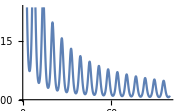

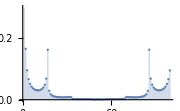

-Graphics-

```mathematica
ysol=NDSolveValue[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,100}];

dft=Abs[Fourier[Table[ysol[x],{x,0,100,1}]]]^2;
Plot[ysol[x],{x,0,100},ImageSize->Small]
ListPlot[dft[[1;;100]],Filling->Axis,PlotRange->{All,{0,0.3}},ImageSize->Small]

MatrixPlot[UnitStep[0.0001-DistanceMatrix[ysol[Range[0,100,.1]]]]]
```